```mathematica
ClearAll;
```

```mathematica
(*SetDirectory[NotebookDirectory[]];<<lce.m*)
```

```mathematica
(*Parameters*)
mu=1.0; (*Solved using constraint on total energy*)
M=1.0;
L=1.0;

z0=0.5;
alpha=0.1; (*Important parameter*)
```

```mathematica
logcosh[x_]:=Module[{s,p},s=Sign[x]*x;
p=Exp[-2*s];
s+Log[1+p]-Log[2]]

H[mu_,ics_,alpha_,z0_,M_]:=Module[{w,z,phi,pw,pz,pphi,L},(*Check if input is a vector (1D case) or matrix (2D case)*)If[VectorQ[ics],(*1D case*){w,z,phi,pw,pz,pphi}=ics,(*2D case (matrix where each row is a phase-space coordinate set)*){w,z,phi,pw,pz,pphi}=Transpose[ics]];
(*Define L in terms of pphi*)L=pphi;
(*Return the energy*)mu*(pw^2/(2*mu)+pz^2/(2*mu)+L^2/(2*mu^2*w^2)-M/Sqrt[w^2+z^2]+alpha*z0*logcosh[z/z0])]
```

```mathematica
(*Initialize ics*)
ics={1.2,0.0,0.0,0.0,0.76,L};

(*Initialize t*)
tspan=Range[0.,100000.,1];
```

```mathematica
(*Define function to evolve the system*)evolve[t_,x_,alpha_,z0_,M_]:=Module[{w,z,phi,pw,pz,pphi,dw,dz,dphi,dpw,dpz,dpphi},{w,z,phi,pw,pz,pphi}=x;
(*Calculate derivatives*)
dw=pw;
dz=pz;
dphi=pphi/(mu*w^2);
dpw=-mu*(-pphi^2/(mu^2*w^3)+M*w/((w^2+z^2)^(3/2)));
dpz=-mu*(M*z/((w^2+z^2)^(3/2))+alpha*Tanh[z/z0]);
dpphi=0.0;
(*Return result as a list (equivalent to np.array in Python)*){dw,dz,dphi,dpw,dpz,dpphi}];
```

```mathematica
Thread[D[{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},t]==evolve[t,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha,z0,M]]
```

{w'[t]==pw[t],z'[t]==pz[t],phi'[t]==(1. pphi[t])/w[t]^2,pw'[t]==-1. (-(1. pphi[t]^2)/w[t]^3+(1. w[t])/((w[t]^2+z[t]^2)^(3/2))),pz'[t]==-1. (0.1 Tanh[2. z[t]]+(1. z[t])/((w[t]^2+z[t]^2)^(3/2))),pphi'[t]==0.}

```mathematica
(*Solve the differential equation system*){sol,pointsData}=Reap@NDSolve[{(*System of differential equations*)Thread[D[{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},t]==evolve[t,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha,z0,M]],(*Initial conditions*)w[0]==ics[[1]],z[0]==ics[[2]],phi[0]==ics[[3]],pw[0]==ics[[4]],pz[0]==ics[[5]],pphi[0]==ics[[6]],(*Poincare section condition*)WhenEvent[z[t]==0 && pz[t]>0,Sow[{w[t],pw[t],H[mu,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha,z0,M]}]]},{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},{t,0,tspan[[-1]]},Method->{"StiffnessSwitching"},AccuracyGoal->11,PrecisionGoal->11];
```

```mathematica
points= pointsData[[1,All,{1,2}]]
```

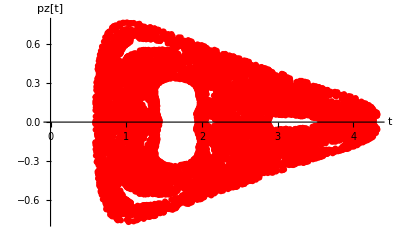

```mathematica
(*Plot the points*)ListPlot[points,PlotStyle->Red,PlotLegends->"Expressions",AxesLabel->{"t","pz[t]"},PlotMarkers->Automatic]
```

```mathematica
Energy=pointsData[[1,All,3]];
```

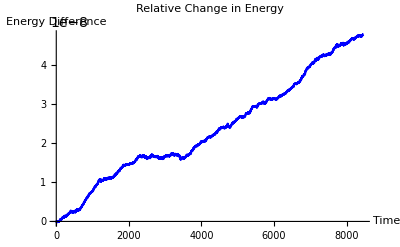

```mathematica
(*Line plot*)ListLinePlot[Energy-Energy[[1]],PlotStyle->Blue,AxesLabel->{"Time","Energy Difference"},PlotLabel->"Relative Change in Energy"]
```

```mathematica
(*Example initial conditions and time*)
ics={1.2,0.0,0.0,0.0,0.76,L};  
(*Generate random normal values for w(0)*)
w0=RandomVariate[NormalDistribution[0,1],6];
(*Normalize w(0) to make it a unitary vector*)
w0=w0/Norm[w0];
(*Combine u0 and w0 into a single flattened vector*)
Y0=Flatten[{ics,w0}]
(*Call the chaoticLyp function*)
(*chaoticLyp[t,Y0,alpha]*)
```

{1.2,0.,0.,0.,0.76,1.,0.0602013,0.215973,0.400738,0.882988,-0.00414236,-0.0972387}

```mathematica
JacobianMatrix[funs_List, vars_List] := Outer[D, funs, vars]
```

```mathematica
J=JacobianMatrix[evolve[0.,{Subscript[y, 1][t],Subscript[y, 2][t],Subscript[y, 3][t],Subscript[y, 4][t],Subscript[y, 5][t],Subscript[y, 6][t]},α,z,Μ],{Subscript[y, 1][t],Subscript[y, 2][t],Subscript[y, 3][t],Subscript[y, 4][t],Subscript[y, 5][t],Subscript[y, 6][t]}]
```

{{0,0,0,1,0,0},{0,0,0,0,1,0},{-(2. y_6[t])/y_1[t]^3,0,0,0,0,1./y_1[t]^2},{-1. (-(3 Μ y_1[t]^2)/((y_1[t]^2+y_2[t]^2)^(5/2))+Μ/((y_1[t]^2+y_2[t]^2)^(3/2))+(3. y_6[t]^2)/y_1[t]^4),(3. Μ y_1[t] y_2[t])/((y_1[t]^2+y_2[t]^2)^(5/2)),0,0,0,(2. y_6[t])/y_1[t]^3},{(3. Μ y_1[t] y_2[t])/((y_1[t]^2+y_2[t]^2)^(5/2)),-1. ((α Sech[y_2[t]/z]^2)/z-(3 Μ y_2[t]^2)/((y_1[t]^2+y_2[t]^2)^(5/2))+Μ/((y_1[t]^2+y_2[t]^2)^(3/2))),0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Y={Subscript[y, 7][t],Subscript[y, 8][t],Subscript[y, 9][t],Subscript[y, 10][t],Subscript[y, 11][t],Subscript[y, 12][t]};
```

```mathematica
E1=Flatten[Transpose[J.Y]];
```

```mathematica
EQ3=Table[D[Subscript[y, i][t],{t,1}]== evolve[0.,{Subscript[y, 1][t],Subscript[y, 2][t],Subscript[y, 3][t],Subscript[y, 4][t],Subscript[y, 5][t],Subscript[y, 6][t]},α,z,Μ][[i]],{i,1,6}]
```

{y_1'[t]==y_4[t],y_2'[t]==y_5[t],y_3'[t]==(1. y_6[t])/y_1[t]^2,y_4'[t]==-1. ((Μ y_1[t])/((y_1[t]^2+y_2[t]^2)^(3/2))-(1. y_6[t]^2)/y_1[t]^3),y_5'[t]==-1. (α Tanh[y_2[t]/z]+(Μ y_2[t])/((y_1[t]^2+y_2[t]^2)^(3/2))),y_6'[t]==0.}

```mathematica
EQ9=Table[D[Subscript[y, i][t],{t,1}]==E1[[i-6]],{i,7,12}]
```

{y_7'[t]==y_10[t],y_8'[t]==y_11[t],y_9'[t]==-(2. y_6[t] y_7[t])/y_1[t]^3+(1. y_12[t])/y_1[t]^2,y_10'[t]==-1. (-(3 Μ y_1[t]^2)/((y_1[t]^2+y_2[t]^2)^(5/2))+Μ/((y_1[t]^2+y_2[t]^2)^(3/2))+(3. y_6[t]^2)/y_1[t]^4) y_7[t]+(3. Μ y_1[t] y_2[t] y_8[t])/((y_1[t]^2+y_2[t]^2)^(5/2))+(2. y_6[t] y_12[t])/y_1[t]^3,y_11'[t]==(3. Μ y_1[t] y_2[t] y_7[t])/((y_1[t]^2+y_2[t]^2)^(5/2))-1. ((α Sech[y_2[t]/z]^2)/z-(3 Μ y_2[t]^2)/((y_1[t]^2+y_2[t]^2)^(5/2))+Μ/((y_1[t]^2+y_2[t]^2)^(3/2))) y_8[t],y_12'[t]==0}

```mathematica
YI12={Subscript[y, 7][0]==w0[[1]],Subscript[y, 8][0]==w0[[2]],Subscript[y, 9][0]==w0[[3]],Subscript[y, 10][0]==w0[[4]],Subscript[y, 11][0]==w0[[5]],Subscript[y, 12][0]==w0[[6]]}
```

{y_7[0]==0.0602013,y_8[0]==0.215973,y_9[0]==0.400738,y_10[0]==0.882988,y_11[0]==-0.00414236,y_12[0]==-0.0972387}

```mathematica
YI6={Subscript[y, 1][0]== ics[[1]],Subscript[y, 2][0]== ics[[2]],Subscript[y, 3][0]== ics[[3]],Subscript[y, 4][0]== ics[[4]],Subscript[y, 5][0]== ics[[5]],Subscript[y, 6][0]== ics[[6]]}
```

{y_1[0]==1.2,y_2[0]==0.,y_3[0]==0.,y_4[0]==0.,y_5[0]==0.76,y_6[0]==1.}

```mathematica
(*Define the chaotic_lyp function in Mathematica*)chaoticLyp[t_,Y_,alpha_]:=Module[{w,z,phi,pw,pz,pphi,dfw,dfz,dfphi,dfpw,dfpz,dfpphi,dfhdwdw,dfhdwdz,dfhdzdz,J,dY,dYdt},(*Unpack Y*){w,z,phi,pw,pz,pphi}=Take[Y,6];
(*System of differential equations*)
dfw=pw;
dfz=pz;
dfphi=pphi/(mu*w^2);
dfpw=-mu*(-pphi^2/(mu^2*w^3)+M*w/((w^2+z^2)^(3/2)));
dfpz=-mu*(M*z/((w^2+z^2)^(3/2))+alpha*Tanh[z/z0]);
dfpphi=0.0;
(*Jacobian matrix elements*)
dfhdwdw=-mu*(3*pphi^2/((mu^2)*(w^4))-3*M*w^2/((w^2+z^2)^(5/2))+M/((w^2+z^2)^(3/2)));
dfhdwdz=3*M*mu*w*z/((w^2+z^2)^(5/2));
dfhdzdz=-mu*(-3*M*z^2/((w^2+z^2)^(5/2))+M/((w^2+z^2)^(3/2))+alpha*(Sech[z/z0]^2)/z0);
(*Jacobian matrix*)J={{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{-2.*L/(mu*w^3.),0.,0.,0.,0.,1./(mu*w^2.)},{dfhdwdw,dfhdwdz,0.,0.,0.,2.*pphi/(mu*w^3.)},{dfhdwdz,dfhdzdz,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}};
(*Extract dY and reshape*)
dY=Drop[Y,6];
(*dY=Drop[Y,6];*)
(*Compute dY_dt*)
dYdt=J.dY;
(*dYdt=Table[Sum[J[[i,j]]*dY[[j]],{j,1,6}],{i,1,6}];*)
(*Concatenate the results and return the final output*)
(*Join[{dfw,dfz,dfphi,dfpw,dfpz,dfpphi},Flatten[dYdt]];*)
Join[{dfw,dfz,dfphi,dfpw,dfpz,dfpphi},dYdt];];
```

```mathematica
(*ClearAll;
(* Get the Lyapunov Exponent of the trajectory*)
tau=50;
{usol,X1t}=Reap@NDSolve[Join[Flatten[{EQ9/.{Μ->M,z->z0,α->alpha},EQ3/.{Μ->M,z->z0,α->alpha},Subscript[y, 1][0]==ics[[1]],Subscript[y, 2][0]==ics[[2]],Subscript[y, 3][0]==ics[[3]],Subscript[y, 4][0]==ics[[4]],Subscript[y, 5][0]==ics[[5]],Subscript[y, 6][0]==ics[[6]],Subscript[y, 7][0]==ics[[7]],Subscript[y, 8][0]==ics[[8]],Subscript[y, 9][0]==ics[[9]],Subscript[y, 10][0]==ics[[10]],Subscript[y, 11][0]==ics[[11]],Subscript[y, 12][0]==ics[[12]],WhenEvent[Mod[t,tau]==0.,{Sow[{Log[Norm[{Subscript[y, 7][t],Subscript[y, 8][t],Subscript[y, 9][t],Subscript[y, 10][t],Subscript[y, 11][t],Subscript[y, 12][t]}]],H[mu,{Subscript[y, 1][t],Subscript[y, 2][t],Subscript[y, 3][t],Subscript[y, 4][t],Subscript[y, 5][t],Subscript[y, 6][t]},alpha,z0,M]}],anorm=Norm[{Subscript[y, 7][t],Subscript[y, 8][t],Subscript[y, 9][t],Subscript[y, 10][t],Subscript[y, 11][t],Subscript[y, 12][t]}],{Subscript[y, 7][t]->Subscript[y, 7][t]/anorm,Subscript[y, 8][t]->Subscript[y, 8][t]/anorm,Subscript[y, 9][t]->Subscript[y, 9][t]/anorm,Subscript[y, 10][t]->Subscript[y, 10][t]/anorm,Subscript[y, 11][t]->Subscript[y, 11][t]/anorm,Subscript[y, 12][t]->Subscript[y, 12][t]/anorm}}]}]],{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],Subscript[y, 10],Subscript[y, 11],Subscript[y, 12]},{t,0.,10000.},Method->{"StiffnessSwitching"},AccuracyGoal->12,PrecisionGoal->12];*)
```

```mathematica
(*X1t*)
```

```mathematica
(*ListLinePlot[X1t[[1,All,2]]-X1t[[1,All,2]][[1]],PlotStyle->Blue,AxesLabel->{"Time","Energy Difference"},PlotLabel->"Relative Change in Energy"]*)
```

```mathematica
(*ListLinePlot[Accumulate[X1t[[1,All,1]]]/Range[tau,100000.,tau],PlotStyle->Blue,AxesLabel->{"Time","Lyapunov Exponent"},PlotLabel->"Lyapunov Exponent"]*)
```

```mathematica
ClearAll;
```

```mathematica
evolveLyap[ics0_,tau_,tf_,alpha_,z0_,M_]:=Module[{ti,timestep,size,X1t,sum,ics,h,sol,traj,timeint,usol,xk,wk,alphak,wk0,i},ti=0.;
timestep=Range[ti,tf,tau];
size=Length[timestep];
X1t=ConstantArray[0.,size-1];
sum=0.;
ics=ics0;
h=ConstantArray[0.,size-1];
(*sol=ConstantArray[0.,{size,6}];
sol[[1]]=Take[ics,6];*)Do[usol=NDSolveValue[Join[Flatten[{EQ9/.{Μ->M,z->z0,α->alpha},EQ3/.{Μ->M,z->z0,α->alpha},Subscript[y, 1][0]==ics[[1]],Subscript[y, 2][0]==ics[[2]],Subscript[y, 3][0]==ics[[3]],Subscript[y, 4][0]==ics[[4]],Subscript[y, 5][0]==ics[[5]],Subscript[y, 6][0]==ics[[6]],Subscript[y, 7][0]==ics[[7]],Subscript[y, 8][0]==ics[[8]],Subscript[y, 9][0]==ics[[9]],Subscript[y, 10][0]==ics[[10]],Subscript[y, 11][0]==ics[[11]],Subscript[y, 12][0]==ics[[12]](*,WhenEvent[Mod[t,tau]==0.,Print[Norm[{Subscript[y, 7][t],Subscript[y, 8][t],Subscript[y, 9][t],Subscript[y, 10][t],Subscript[y, 11][t],Subscript[y, 12][t]}]]]*)}]],{Subscript[y, 1][timestep[[i+1]]],Subscript[y, 2][timestep[[i+1]]],Subscript[y, 3][timestep[[i+1]]],Subscript[y, 4][timestep[[i+1]]],Subscript[y, 5][timestep[[i+1]]],Subscript[y, 6][timestep[[i+1]]],Subscript[y, 7][timestep[[i+1]]],Subscript[y, 8][timestep[[i+1]]],Subscript[y, 9][timestep[[i+1]]],Subscript[y, 10][timestep[[i+1]]],Subscript[y, 11][timestep[[i+1]]],Subscript[y, 12][timestep[[i+1]]]},{t,timestep[[i]],timestep[[i+1]]},Method->{"StiffnessSwitching"},AccuracyGoal->12,PrecisionGoal->12];
(*usol=(#[timestep[[i+1]]]&)/@usol;*)
xk=Take[usol,6];
wk=Drop[usol,6];
alphak=Norm[wk];
sum+=Log[alphak];
X1t[[i]]=sum/timestep[[i+1]];
wk0=wk/alphak;
ics=Join[xk,wk0];
(*YI3={Subscript[y, 1][0]== ics[[1]],Subscript[y, 2][0]== ics[[2]],Subscript[y, 3][0]== ics[[3]],Subscript[y, 4][0]== ics[[4]],Subscript[y, 5][0]== ics[[5]],Subscript[y, 6][0]== ics[[6]]};
YI9={Subscript[y, 7][0]==ics[[7]],Subscript[y, 8][0]==ics[[8]],Subscript[y, 9][0]==ics[[9]],Subscript[y, 10][0]==ics[[10]],Subscript[y, 11][0]==ics[[11]],Subscript[y, 12][0]==ics[[12]]};*)
(*Sanity Check*)h[[i]]=H[1.00,xk,alpha,z0,M];
(*sol[[i+1]]=Take[ics,6];*),{i,1,size-1}];
{X1t,h}]
```

```mathematica
(*i=2;
timestep=Range[0.,10000.,1000];
usol=NDSolveValue[Join[Flatten[{EQ9,EQ3,Subscript[y, 1][0]==Y0[[1]],Subscript[y, 2][0]==Y0[[2]],Subscript[y, 3][0]==Y0[[3]],Subscript[y, 4][0]==Y0[[4]],Subscript[y, 5][0]==Y0[[5]],Subscript[y, 6][0]==Y0[[6]],Subscript[y, 7][0]==Y0[[7]],Subscript[y, 8][0]==Y0[[8]],Subscript[y, 9][0]==Y0[[9]],Subscript[y, 10][0]==Y0[[10]],Subscript[y, 11][0]==Y0[[11]],Subscript[y, 12][0]==Y0[[12]]}]],{Subscript[y, 1][timestep[[i+1]]],Subscript[y, 2][timestep[[i+1]]],Subscript[y, 3][timestep[[i+1]]],Subscript[y, 4][timestep[[i+1]]],Subscript[y, 5][timestep[[i+1]]],Subscript[y, 6][timestep[[i+1]]],Subscript[y, 7][timestep[[i+1]]],Subscript[y, 8][timestep[[i+1]]],Subscript[y, 9][timestep[[i+1]]],Subscript[y, 10][timestep[[i+1]]],Subscript[y, 11][timestep[[i+1]]],Subscript[y, 12][timestep[[i+1]]]},{t,timestep[[i]],timestep[[i+1]]},Method->{"StiffnessSwitching"},AccuracyGoal->12,PrecisionGoal->12]*)
```

```mathematica
lyaps=evolveLyap[Y0,50,20000.,alpha,z0,M];
```

General::munfl: 2.11558×10^-21 (-3.76088×10^-293) is too small to represent as a normalized machine number; precision may be lost.

```mathematica
sum=0.;
timestep=Range[0.,200.,50];evolveStep[{ics_,sum_},time_]:=Module[{usol,xk,wk,alphak,wk0,h},usol=NDSolveValue[Join[Flatten[{EQ9/.{Μ->M,z->z0,α->alpha},EQ3/.{Μ->M,z->z0,α->alpha},Subscript[y, 1][0]==ics[[1]],Subscript[y, 2][0]==ics[[2]],Subscript[y, 3][0]==ics[[3]],Subscript[y, 4][0]==ics[[4]],Subscript[y, 5][0]==ics[[5]],Subscript[y, 6][0]==ics[[6]],Subscript[y, 7][0]==ics[[7]],Subscript[y, 8][0]==ics[[8]],Subscript[y, 9][0]==ics[[9]],Subscript[y, 10][0]==ics[[10]],Subscript[y, 11][0]==ics[[11]],Subscript[y, 12][0]==ics[[12]](*,WhenEvent[Mod[t,tau]==0.,Print[Norm[{Subscript[y, 7][t],Subscript[y, 8][t],Subscript[y, 9][t],Subscript[y, 10][t],Subscript[y, 11][t],Subscript[y, 12][t]}]]]*)}]],{Subscript[y, 1][time],Subscript[y, 2][time],Subscript[y, 3][time],Subscript[y, 4][time],Subscript[y, 5][time],Subscript[y, 6][time],Subscript[y, 7][time],Subscript[y, 8][time],Subscript[y, 9][time],Subscript[y, 10][time],Subscript[y, 11][time],Subscript[y, 12][time]},{t,time-50,time},Method->{"StiffnessSwitching"},AccuracyGoal->12,PrecisionGoal->12];
(*Extract results and compute*)xk=Take[usol,6];
wk=Drop[usol,6];
alphak=Norm[wk];
(*sum=sum+Log[alphak];*)
wk0=wk/alphak;
{Join[xk,wk0],sum+Log[alphak]}];
FoldList[evolveStep,{Y0,sum},Rest[timestep]]
```

{{{1.2,0.,0.,0.,0.76,1.,0.0602013,0.215973,0.400738,0.882988,-0.00414236,-0.0972387},0.},{{2.72948,0.990552,19.9765,0.131863,0.108941,1.,0.406565,-0.102405,0.876565,-0.229123,0.0520703,-0.0253524},1.34429},{{1.0301,0.346672,57.9622,0.116205,-0.683579,1.,0.00332831,-0.449292,0.850485,0.202882,-0.183409,-0.001032},4.54567},{{1.10287,-0.790995,115.063,-0.322679,0.244342,1.,0.369345,-0.123775,-0.858101,-0.301523,-0.144951,-0.00011058},6.77918},{{0.955463,0.0358041,192.536,0.176639,-0.755168,1.,0.240838,-0.408165,0.859559,0.19119,0.00169906,-6.61631×10^-8},14.2006}}

```mathematica
X1t=MapIndexed[#1[[2]]/timestep[[#2[[1]]+1]]&,Rest[FoldList[evolveStep,{Y0,sum},Rest[timestep]]]]
```

{0.0268859,0.0454567,0.0451946,0.0710028}

```mathematica
FevolveLyap[ics0_,tau_,tf_,alpha_,z0_,M_]:=Module[{timestep,size,X1t,sum,compiledFunc,evolveStep},timestep=Range[0.,tf,tau];
size=Length[timestep];
X1t=ConstantArray[0.,size-1];
(*compiledFunc=(*Define the compiled function here as in your code*);*)
(*Define a single evolution step*)

sum=0.;evolveStep[{ics_,sum_},time_]:=Module[{usol,xk,wk,alphak,wk0,h},usol=NDSolveValue[Join[Flatten[{EQ9/.{Μ->M,z->z0,α->alpha},EQ3/.{Μ->M,z->z0,α->alpha},Subscript[y, 1][0]==ics[[1]],Subscript[y, 2][0]==ics[[2]],Subscript[y, 3][0]==ics[[3]],Subscript[y, 4][0]==ics[[4]],Subscript[y, 5][0]==ics[[5]],Subscript[y, 6][0]==ics[[6]],Subscript[y, 7][0]==ics[[7]],Subscript[y, 8][0]==ics[[8]],Subscript[y, 9][0]==ics[[9]],Subscript[y, 10][0]==ics[[10]],Subscript[y, 11][0]==ics[[11]],Subscript[y, 12][0]==ics[[12]](*,WhenEvent[Mod[t,tau]==0.,Print[Norm[{Subscript[y, 7][t],Subscript[y, 8][t],Subscript[y, 9][t],Subscript[y, 10][t],Subscript[y, 11][t],Subscript[y, 12][t]}]]]*)}]],{Subscript[y, 1][time],Subscript[y, 2][time],Subscript[y, 3][time],Subscript[y, 4][time],Subscript[y, 5][time],Subscript[y, 6][time],Subscript[y, 7][time],Subscript[y, 8][time],Subscript[y, 9][time],Subscript[y, 10][time],Subscript[y, 11][time],Subscript[y, 12][time]},{t,time-50,time},Method->{"StiffnessSwitching"},AccuracyGoal->12,PrecisionGoal->12];
(*Extract results and compute*)xk=Take[usol,6];
wk=Drop[usol,6];
alphak=Norm[wk];
(*sum=sum+Log[alphak];*)
wk0=wk/alphak;
{Join[xk,wk0],sum+Log[alphak]}];
(*Use FoldList to propagate the state*)FoldList[evolveStep,{ics0,sum},Rest[timestep]];
(*Extract the Lyapunov exponent estimates*)X1t=MapIndexed[#1[[2]]/timestep[[#2[[1]]+1]]&,Rest[FoldList[evolveStep,{Y0,sum},Rest[timestep]]]];
X1t]
```

```mathematica
FevolveLyap[Y0,100,10000.,10.,z0,M]
```

{0.0261316,0.0188163,0.0156553,0.0136559,0.0108756,0.00941928,0.00927173,0.00774538,0.00758329,0.0066294,0.00669073,0.00580661,0.0055867,0.00558783,0.00513472,0.00473409,0.00447069,0.00428668,0.00411643,0.00396033,0.00386001,0.00383744,0.0038281,0.00353095,0.00335295,0.00347206,0.00316742,0.00321325,0.00300452,0.00310196,0.00283685,0.00282883,0.00287951,0.00272373,0.00259287,0.00251563,0.0024638,0.00241338,0.0023621,0.00233555,0.00234589,0.00237671,0.00224701,0.00215445,0.00223895,0.00209463,0.00211818,0.00202817,0.00208597,0.00194586,0.00196542,0.0019993,0.00189937,0.00183154,0.00180174,0.00177894,0.00175338,0.00172546,0.00170691,0.00171604,0.00175125,0.00168839,0.00161353,0.0016698,0.00159845,0.00159605,0.00156032,0.00158718,0.00149906,0.00153768,0.00154352,0.00146982,0.00143233,0.00142098,0.00141083,0.001397,0.00137698,0.00135786,0.00136075,0.00139199,0.0013733,0.00130557,0.00133597,0.00131054,0.00128501,0.00128601,0.00128244,0.00123311,0.00127617,0.00125575,0.0012036,0.00118639,0.00118364,0.00118201,0.00117173,0.00115592,0.00113634,0.00113134,0.00115321,0.00116464}